```mathematica
SetDirectory["~/Cellular-Automata"];
Width=32;
Height=64;
seed=0;
uniqueRuleTable={0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,18,19,22,23,24,25,26,27,28,29,30,32,33,34,35,36,37,38,40,41,42,43,44,45,46,50,51,54,56,57,58,60,62,72,73,74,76,77,78,90,94,104,105,106,108,110,122,126,128,130,132,134,136,138,140,142,146,150,152,154,156,160,162,164,168,170,172,178,184,200,204,232};
makePic[Width_,Height_,data_,isExpanding_]:=Table[{If[data[[j,i]]==1,Black,White],Polygon[{{i,-j},{i+1,-j},{(data[[j+1,Width+1]]-1)(i+1)-(data[[j+1,Width+1]]-2)(Width/2+1),-j-1},{(data[[j+1,Width+1]]-1)(i)-(data[[j+1,Width+1]]-2)(Width/2+1),-j-1}}]},{i,1,Width},{j,1, (1+isExpanding/4)(Height-1)}];
Run["./RunSim -f -b -e 1"];
data=Import["./30_time_series_seed_"<>ToString[seed]<>".csv"];
infoData=Import["./30_info_series_seed_"<>ToString[seed]<>".csv"];
```

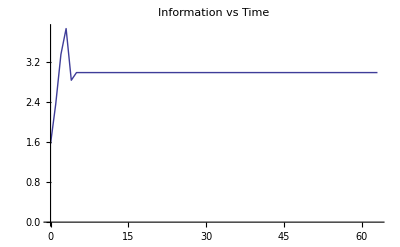

```mathematica
ListPlot[infoData,Joined->True,PlotLabel->"Information vs Time"]
```

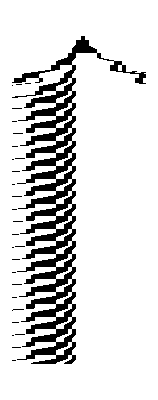

```mathematica
pic=makePic[Width,Height,data,1];
(*Export["rule_num_30.gif",Graphics[pic,PlotRange->{{1,17},All}]]*)
Graphics[pic,PlotRange->{{1,Width},All}]
```

```mathematica
Do[
data=Import["./"<>ToString[uniqueRuleTable[[k]]]<>"_time_series_seed_"<>ToString[seed]<>".csv"];
Export[ToString[uniqueRuleTable[[k]]]<>"_time.gif",
Graphics[makePic[Width,Height,data,1],
PlotRange->{{1,Width+1},All}]],{k,1,88,1}];
Do[
infoData=Import["./"<>ToString[uniqueRuleTable[[k]]]<>"_info_series_seed_"<>ToString[seed]<>".csv"];Export[ToString[uniqueRuleTable[[k]]]<>"_info.gif",
ListPlot[infoData,Joined->True,PlotLabel->"Information vs Time for Rule "<>ToString[uniqueRuleTable[[k]]]]],{k,1,88,1}];
```